# Exact Bounce Quartic Potential

Bounce

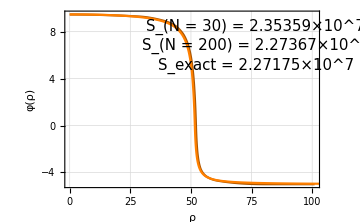

```mathematica
SetDirectory[FileNameTake[NotebookDirectory[],{1,-4}]];
<<"FindBounce.m"
Module[{ϵ = 1,Vt=5,ϕm=10,Vm=-20,ϕp=-5,Vp,ΔVp,ΔVm,α,Δ,Rt,A},
	Vp = -18+(ϵ-1)*3;
	ΔVm=Vt-Vm;
	ΔVp= Vt - Vp;
	α = -ϕp/ϕm;
	Δ = ΔVp/ΔVm;
	Rt = Sqrt[2 (1 + α)(α+Δ)]/(1 - Δ)ϕm/Sqrt[Vm];
	A = (1 + Sqrt[1 + 2 ΔVp Rt^2/ϕp^2])/( ΔVp Rt^2/ϕp^3);
	Extrema ={ϕp,0,ϕm} ;
	U[ϕ_] :=Piecewise[{{(Vp + ΔVp/ϕp^4 (ϕ-ϕp)^4)-Vp ,ϕ<0},{(Vm+  ΔVm/ϕm^4 (ϕ-ϕm)^4)-Vp,ϕ≥ 0}}];
	ActionExact =((2 π^2 ϕm^4)/(3ΔVm)) (4 α^3 + 6 α^2 Δ + 4α Δ^2+Δ^3+α^4(3+Δ(Δ -3)))/(1 - Δ)^3;
];
PBDefault =  FindBounce[ U[ϕ],{ϕ},{Extrema[[1]],Extrema[[3]]},"InitialFieldValue"->Extrema[[2]],"MethodSegmentation"->"HSPlus","Improvement"->False];
PB200 =  FindBounce[ U[ϕ],{ϕ},{Extrema[[1]],Extrema[[3]]},"InitialFieldValue"->Extrema[[2]],"Segments"->200,"MethodSegmentation"->"HSPlus","Improvement"->False];
Row[{"Exact Action = ",N@ActionExact}];
Show[{BouncePlot[PBDefault,PlotStyle->Darker@Orange],BouncePlot[PB200]},
ImageSize->Medium,
Epilog->{Text[Style[Row[{"S_(N = 30) = ",PBDefault["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.91}],Background->LightGreen],
Text[Style[Row[{"S_(N = 200) = ",PB200["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.8}],Background->LightGreen],
Text[Style[Row[{"S_exact = ",N@ActionExact}],10,15,"Times New Roman"],Scaled[{0.75,0.69}],Background->LightRed]}]
```

Potential

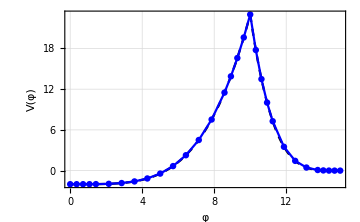

```mathematica
plotU = Plot[U[Extrema[[3]]-ϕ],{ϕ,0,Abs@Extrema[[1]]+Abs@Extrema[[3]]},
	PlotStyle->{Black,Dashed},
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False
];
Show[plotU,ListPlot[Transpose@{PBDefault["PathLongitudinal"],PBDefault["Potential"]},Joined->True,Mesh->All,PlotStyle->Blue]]
```